NEWTON-RAPHSON METHOD :_

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_]:=x^3-2x-5
```

```mathematica
Solve[f[x]==0]//N
```

{{x→2.09455},{x→-1.04728+1.13594 ⅈ},{x→-1.04728-1.13594 ⅈ}}

```mathematica
h=0.1; x[0]=1;
```

```mathematica
Do[x[n]=N[x[n-1]-f[x[n-1]]/f'[x[n-1]]], {n,1,11}]
```

```mathematica
num=Table[n,{n,0,11}]
```

{0,1,2,3,4,5,6,7,8,9,10,11}

```mathematica
tab1=Table[{num[[i]],x[i-1]},{i,1,12}]
```

{{0,1},{1,7.},{2,4.76552},{3,3.3487},{4,2.5316},{5,2.17392},{6,2.09788},{7,2.09456},{8,2.09455},{9,2.09455},{10,2.09455},{11,2.09455}}

```mathematica
tab2=Prepend[tab1,{"Num(n)","Xn"}]
```

{{Num(n),Xn},{0,1},{1,7.},{2,4.76552},{3,3.3487},{4,2.5316},{5,2.17392},{6,2.09788},{7,2.09456},{8,2.09455},{9,2.09455},{10,2.09455},{11,2.09455}}

```mathematica
Grid[tab2,Spacings->{1, 1},Frame->All]
```

Num(n) | Xn
0 | 1
1 | 7.
2 | 4.76552
3 | 3.3487
4 | 2.5316
5 | 2.17392
6 | 2.09788
7 | 2.09456
8 | 2.09455
9 | 2.09455
10 | 2.09455
11 | 2.09455

EULER METHOD :_

```mathematica
f[x_,y_]:=x^2-y
```

```mathematica
h=0.1; x[0]=0; y[0]=1;
```

```mathematica
Do[Print[{x[n]=n h,
y[n]=N[y[n-1]+h f[x[n-1],y[n-1]]]}],
{n,1,10}]
```

{0.1,0.9}

{0.2,0.811}

{0.3,0.7339}

{0.4,0.66951}

{0.5,0.618559}

{0.6,0.581703}

{0.7,0.559533}

{0.8,0.55258}

{0.9,0.561322}

{1.,0.586189}

```mathematica
Num=Table[y[n],{n,0,10}]
```

{1,0.9,0.811,0.7339,0.66951,0.618559,0.581703,0.559533,0.55258,0.561322,0.586189}

```mathematica
x=Table[x,{x,0,1,0.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
ex=x^2-2x+2-Exp[-x]
```

{1.,0.905163,0.821269,0.749182,0.68968,0.643469,0.611188,0.593415,0.590671,0.60343,0.632121}

```mathematica
tab1=Table[{x[[i]],Num[[i]],ex[[i]],ScientificForm[Abs[Num[[i]]-ex[[i]]]]},{i,1,11}]
```

{{0.,1,1.,0.},{0.1,0.9,0.905163,5.16258×10^-3},{0.2,0.811,0.821269,1.02692×10^-2},{0.3,0.7339,0.749182,1.52818×10^-2},{0.4,0.66951,0.68968,2.017×10^-2},{0.5,0.618559,0.643469,2.49103×10^-2},{0.6,0.581703,0.611188,2.94853×10^-2},{0.7,0.559533,0.593415,3.38819×10^-2},{0.8,0.55258,0.590671,3.80915×10^-2},{0.9,0.561322,0.60343,4.21088×10^-2},{1.,0.586189,0.632121,4.59312×10^-2}}

```mathematica
tab2=Prepend[tab1,{"x","y","Exact","Error"}]
```

{{x,y,Exact,Error},{0.,1,1.,0.},{0.1,0.9,0.905163,5.16258×10^-3},{0.2,0.811,0.821269,1.02692×10^-2},{0.3,0.7339,0.749182,1.52818×10^-2},{0.4,0.66951,0.68968,2.017×10^-2},{0.5,0.618559,0.643469,2.49103×10^-2},{0.6,0.581703,0.611188,2.94853×10^-2},{0.7,0.559533,0.593415,3.38819×10^-2},{0.8,0.55258,0.590671,3.80915×10^-2},{0.9,0.561322,0.60343,4.21088×10^-2},{1.,0.586189,0.632121,4.59312×10^-2}}

```mathematica
Grid[tab2,Spacings->{1, 1},Frame->All]
```

x | y | Exact | Error
0. | 1 | 1. | 0.
0.1 | 0.9 | 0.905163 | 5.16258×10^-3
0.2 | 0.811 | 0.821269 | 1.02692×10^-2
0.3 | 0.7339 | 0.749182 | 1.52818×10^-2
0.4 | 0.66951 | 0.68968 | 2.017×10^-2
0.5 | 0.618559 | 0.643469 | 2.49103×10^-2
0.6 | 0.581703 | 0.611188 | 2.94853×10^-2
0.7 | 0.559533 | 0.593415 | 3.38819×10^-2
0.8 | 0.55258 | 0.590671 | 3.80915×10^-2
0.9 | 0.561322 | 0.60343 | 4.21088×10^-2
1. | 0.586189 | 0.632121 | 4.59312×10^-2

```mathematica
P1=ListPlot[Num, PlotStyle->Red]; P2=ListLinePlot[ex];
```

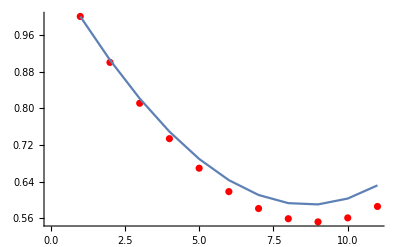

```mathematica
Show[P1,P2]
```

```mathematica
point[a_,b_,c_]:=If[a>b&&a>c, Print[" a is greater then" b "and" c],
If[a<b&&a<c, Print[" 'a' is smaller then `b` and `c`",{a,b,c}],
If[a==b&&a > c, Print[a "and" b "are equal and" c "is smaller"],Print[a "and" b "are equal and" c "is greater"]]]]
```

```mathematica
point[3,5,7]
```

'a' is smaller then `b` and `c`{3,5,7}